```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
```

# Behavior of Holographic Complexity

## Initial Setup

Here we setup initial assumptions etc.

```mathematica
assum = {r>rh>rb>0,a>0,T>0,L>0,gs>0,1>xb>0};
```

```mathematica
(*f function*)
```

```mathematica
f[r_]=r^2(1-rh^4/r^4);
```

```mathematica
(*Temperature*)
```

```mathematica
Temp[L_,rh_]=Assuming[assum,FullSimplify[D[f[r],r]/(4π)/.{r->rh}]]
```

rh/π

### Write down complexification rate and undimensionalize it

We choose to undimensionalize be defining the dimensionless parameters b = a * rh = π a T, rb = xb rh, γ = (α √gs)/(L^2 rh^4). Using these, the only dimensionful parameter left is T, and by normalizing by the commutative late time result we should be able to eliminate this dependence as well.

```mathematica
(*Rate of complexifcation (up to a factor) when the corner is at radius r_B = \rho_B * rh *)
```

```mathematica
Srate[rb_,rh_,a_,α_,L_,gs_]= L^8/gs^2(-(2Log[1+a^4 rb^4])/a^4+4 rb^4+6 rh^4+3(rh^4-rb^4)Log[α/L^2 √gs rb^2/((1+a^4 rb^4)^(1/4)(rh^4-rb^4))]);
```

```mathematica
(*Complexification rate as a genuine function of time*)
```

```mathematica
Srate2[xb_,T_,b_,γ_,L_,gs_]=Assuming[assum,FullSimplify[Srate[π T xb,π T,b/(π T),(γ π^2 L^2 T^2)/(√gs),L,gs]]]
```

(L^8 π^4 T^4 (-2 Log[1+b^4 xb^4]+b^4 (6+4 xb^4-3 (-1+xb^4) Log[(xb^2 γ)/((1-xb^4) (1+b^4 xb^4)^(1/4))])))/(b^4 gs^2)

```mathematica
Sdd[xb_,T_,b_,γ_,L_,gs_] = FullSimplify[-2f[r]D[Srate2[r/(π T),T,b,γ,L,gs],r]/.{r-> π xb T,rh->π T}]
```

(2 L^8 π^5 T^5 (-1+xb^4) (-6-xb^4 (14+b^4 (3+25 xb^4))+12 (xb^4+b^4 xb^8) Log[(xb^2 γ)/((1-xb^4) (1+b^4 xb^4)^(1/4))]))/(gs^2 xb^3 (1+b^4 xb^4))

```mathematica
(*Notice that the dependence on everything but xb, b, and γ becomes an overall factor. Define this as an expression for runtime purposes*)
```

```mathematica
SrateExp = Srate2[xb,T,b,γ,L,gs]
```

(L^8 π^4 T^4 (-2 Log[1+b^4 xb^4]+b^4 (6+4 xb^4-3 (-1+xb^4) Log[(xb^2 γ)/((1-xb^4) (1+b^4 xb^4)^(1/4))])))/(b^4 gs^2)

```mathematica
(*Late time and commutative limits*)
```

```mathematica
SrateLate[T_,b_,α_,L_,gs_]:=Limit[Srate2[xb,T,b,α,L,gs],xb->1]
```

```mathematica
SrateComm[xb_,T_,α_,L_,gs_]:= Limit[Srate2[xb,T,b,α,L,gs],b->0]
```

```mathematica
SrateLateComm[T_,α_,L_,gs_]:=Limit[SrateComm[xb,T,α,L,gs],xb->1]
```

```mathematica
SrateCommLate[T_,α_,L_,gs_]:=Limit[SrateLate[T,b,α,L,gs],b->0]
```

```mathematica
SrateLateComm[T,γ,L,gs]
```

(8 L^8 π^4 T^4)/gs^2

```mathematica
SrateCommLate[T,γ,L,gs]
```

(8 L^8 π^4 T^4)/gs^2

```mathematica
(*Normalize Srate by commutative late time result*)
```

```mathematica
SrateNormalizedExp= Assuming[assum,FullSimplify[(SrateExp/.{L->1,T->1,gs->1})/SrateLateComm[1,γ,1,1]]]
```

(-2 Log[1+b^4 xb^4]+b^4 (6+4 xb^4-3 (-1+xb^4) Log[(xb^2 γ)/((1-xb^4) (1+b^4 xb^4)^(1/4))]))/(8 b^4)

```mathematica
SrateNormalized[xbb_,bb_,γg_]=SrateNormalizedExp/.{xb->xbb,b->bb,γ->γg};
```

```mathematica
SrateNormalized[xb,b,γ]
```

(-2 Log[1+b^4 xb^4]+b^4 (6+4 xb^4-3 (-1+xb^4) Log[(xb^2 γ)/((1-xb^4) (1+b^4 xb^4)^(1/4))]))/(8 b^4)

```mathematica
SddNormalized[xb_,b_,γ_] = Assuming[assum,FullSimplify[Sdd[xb,T,b,γ,L,gs]/(T SrateLateComm[T,γ,L,gs])]]
```

(π (-1+xb^4) (-6-xb^4 (14+b^4 (3+25 xb^4))+12 (xb^4+b^4 xb^8) Log[(xb^2 γ)/((1-xb^4) (1+b^4 xb^4)^(1/4))]))/(4 (xb^3+b^4 xb^7))

```mathematica
SrateTrans[xb_,b_,γ_] = Assuming[assum,FullSimplify[SrateNormalized[xb,b,γ]-SrateLate[T,b,γ,L,gs]/SrateLateComm[T,γ,L,gs]]]
```

(2 Log[1+b^4]-2 Log[1+b^4 xb^4]+b^4 (-1+xb^4) (4-3 Log[(xb^2 γ)/((1-xb^4) (1+b^4 xb^4)^(1/4))]))/(8 b^4)

## The Tortoise Coordinate

Here we find the tortoise coordinate as a function of r, and invert that function for later use.

```mathematica
(*Tortoise coordinate*)
```

```mathematica
rPreStar = Assuming[assum,FullSimplify[Integrate[1/f[r],r]/.{r->x rh}]]
```

(ArcTan[x]-ArcTanh[x])/(2 rh)

```mathematica
(*Fix tortoise coord*)
```

```mathematica
Limit[rPreStar,x->1]
```

(-∞)/rh

```mathematica
rStarShift = Assuming[assum,FullSimplify[Limit[rPreStar,x->∞]]]
```

((1/4+ⅈ/4) π)/rh

```mathematica
rStar = Assuming[assum,FullSimplify[rPreStar-rStarShift]]
```

-((1+ⅈ) π-2 ArcTan[x]+2 ArcTanh[x])/(4 rh)

```mathematica
rPreStar/.{rh->1,x->0.5}
```

-0.0428293

```mathematica
rPreStar/.{rh->1,x->1.5}
```

0.0890374+0.785398 ⅈ

```mathematica
rStar/.{rh->1,x->0.5}
```

-0.828227-0.785398 ⅈ

```mathematica
rStar/.{rh->1,x->1.5}
```

-0.696361+0. ⅈ

```mathematica
(*Invert rStar[r] with an interpolating function*)
```

```mathematica
tList1 = Table[{rPreStar/.{rh->1,x->Exp[Log[1.1]a]},Exp[Log[1.1]a]},{a,-100,-0.01,0.01}];
tList2 = Table[{rPreStar/.{rh->1,x->Exp[Log[1.1]a]},Exp[Log[1.1]a]},{a,-0.008,-0.00001,0.00001}];
tList3 = Table[{rPreStar/.{rh->1,x->Exp[Log[1.1]a]},Exp[Log[1.1]a]},{a,-10^-8,-10^-12,10^-12}];
tList4 = Table[{rPreStar/.{rh->1,x->Exp[Log[1.1]a]},Exp[Log[1.1]a]},{a,-10^-15,-10^-20,10^-20}];
tList5 = Table[{x,1},{x,-10015,-15,1}];
```

```mathematica
tList=Union[tList1,tList2,tList3,tList4,tList5];
tList=DeleteDuplicates[tList];
tList = DeleteCases[tList,{Indeterminate,1.}];
```

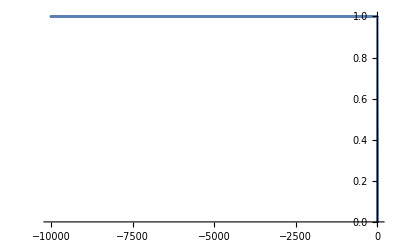

```mathematica
ListPlot[tList,PlotRange->All]
```

```mathematica
ListPlot[tList]
```

-Graphics-

```mathematica
xxInter = Interpolation[tList];
```

```mathematica
xx[x_] := Piecewise[{{1,x<-10100}},xxInter[x]]
```

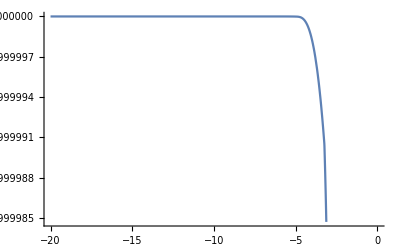

```mathematica
Plot[xx[x],{x,-20,0}]
```

```mathematica
Plot[rPreStar/.{rh->1},{r,-1,1}]
```

-Graphics-

```mathematica
(*xb as a function of t_L assuming t_R = 0*)
```

```mathematica
xxb[t_,T_]:=xx[(-t π T)/2]
```

```mathematica
(*Undimensionalize with τ = t T*)
xxb2[τ_]:=xx[(-π τ)/2]
```

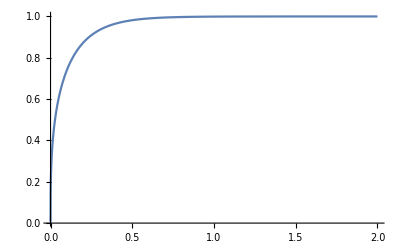

```mathematica
Plot[xxb[t,1],{t,0,2},PlotRange->All]
```

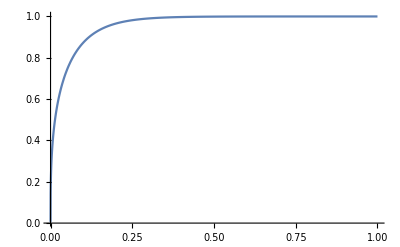

```mathematica
Plot[xxb[t,2],{t,0,1},PlotRange->All]
```

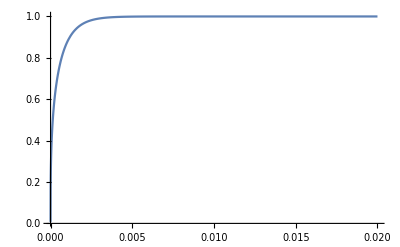

```mathematica
Plot[xxb[t,200],{t,0,0.02},PlotRange->All]
```

## Holographic Complexity as a Function of Time

Here we write down the formula for the complexification rate and observe it’s finite time behavoir

```mathematica
(*Put in thermal time τ = t/β*)
```

```mathematica
SrateNormalized2 [τ_,b_,γ_]=SrateNormalized[xxb2[τ],b,γ];
```

```mathematica
SddNormalized2 [τ_,b_,γ_] = SddNormalized[xxb2[τ],b,γ];
```

```mathematica
SrateTrans2[t_,b_,γ_] = SrateTrans[xxb2[t],b,γ];
```

```mathematica
SddNormalized2[5,100.,1]
```

-1.39938×10^-10

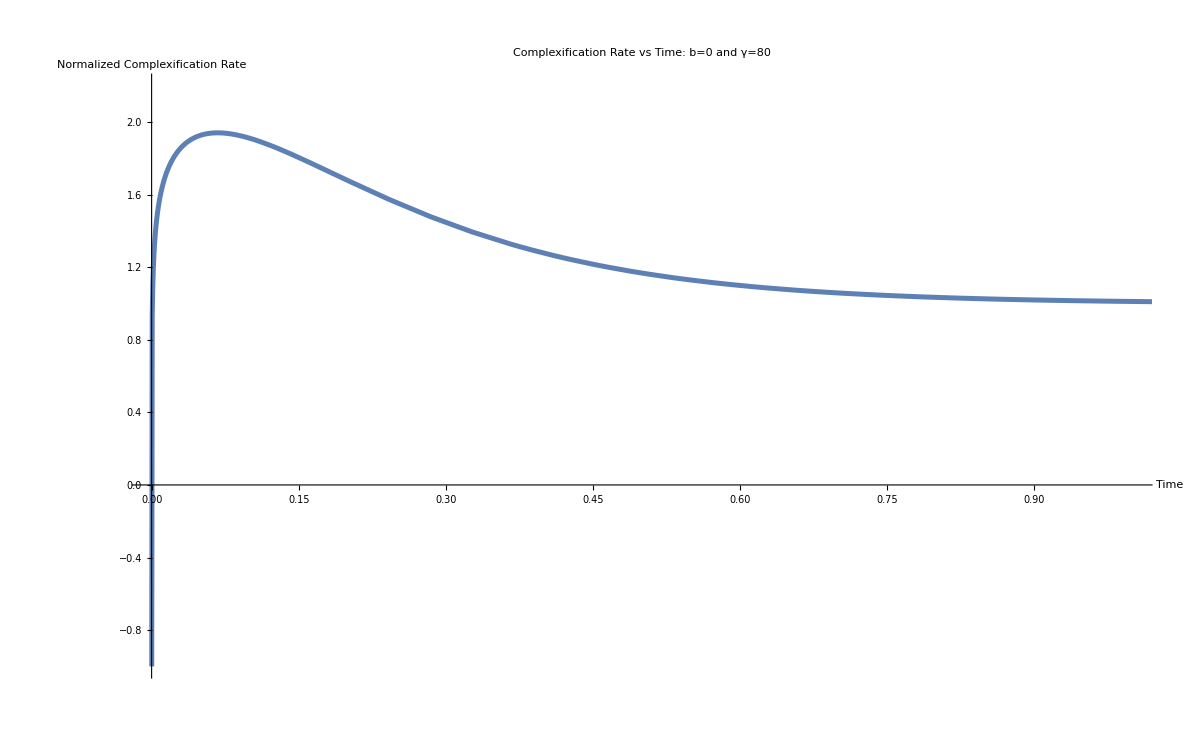

```mathematica
plt1 =Plot[Limit[SrateNormalized2[t,a,80],a->0],{t,0,2},PlotLabel->"Complexification Rate vs Time: b=0 and γ=80",PlotRange->{{0,1},{-1,2.2}},AxesLabel->{"Time","Normalized Complexification Rate"},BaseStyle-> {FontWeight->Bold,FontSize->16},AxesStyle->Thick,ImageSize->1200,PlotStyle-> {Thickness[0.003]}]
```

```mathematica
Export["images/FiniteTime1.pdf",plt1];
```

### Finite time behavoir while varying b and fixing γ

```mathematica
pltb0 = Plot[SrateNormalized2 [t,10^-3,80],{t,0,20},PlotStyle->Red,PlotRange->All,PlotLegends-> Placed[LineLegend[{"b = 10^-3"}],Right]];
pltb1 = Plot[SrateNormalized2 [t,1,80],{t,0,20},PlotStyle->Orange,PlotRange->All,PlotLegends-> Placed[LineLegend[{"b = 1"}],Right]];pltb2 = Plot[SrateNormalized2 [t,1.5,80],{t,0,20},PlotStyle->Yellow,PlotRange->All,PlotLegends-> Placed[LineLegend[{"b = 1.5"}],Right]];pltb3 = Plot[SrateNormalized2 [t,2,80],{t,0,20},PlotStyle->Green,PlotRange->All,PlotLegends-> Placed[LineLegend[{"b = 2"}],Right]];pltb4 = Plot[SrateNormalized2 [t,10^1,80],{t,0,20},PlotStyle->Blue,PlotRange->All,PlotLegends-> Placed[LineLegend[{"b = 10"}],Right]];pltb5 = Plot[SrateNormalized2 [t,10^2,80],{t,0,20},PlotStyle->Purple,PlotRange->All,PlotLegends-> Placed[LineLegend[{"b = 100"}],Right]];pltb6 = Plot[SrateNormalized2 [t,10^3,80],{t,0,20},PlotStyle->Black,PlotRange->All,PlotLegends-> Placed[LineLegend[{"b = 1000"}],Right]];
```

```mathematica
plt2 = Rasterize[Show[pltb0,pltb1,pltb2,pltb3,pltb4,pltb5,pltb6,PlotRange->{{0,1},{0,2}},PlotLabel->"Complexification Rate vs Time Varying b: γ=80",AxesLabel->{"Time","Normalized Complexification Rate"},BaseStyle-> {FontWeight->Bold,FontSize->16},AxesStyle->Thick,ImageSize->1200,PlotStyle-> {Thickness[0.003]}]]
```

OptionValue::nodef: Unknown option "PlotStyle" for Graphics.

-Graphics-

```mathematica
Export["images/vary_b_fix_gamma.pdf",plt2];
```

### Finite time behavoir while varying γ and fixing b

```mathematica
pltg0 = Plot[SrateNormalized2 [t,1,10^-6],{t,0,20},PlotStyle->Red,PlotRange->All,PlotLegends-> Placed[LineLegend[{"γ = 10^-6"}],Right]];
pltg1 = Plot[SrateNormalized2 [t,1,10^-5],{t,0,20},PlotStyle->Orange,PlotRange->All,PlotLegends-> Placed[LineLegend[{"γ = 10^-5"}],Right]];pltg2 = Plot[SrateNormalized2 [t,1,10^-4],{t,0,20},PlotStyle->Yellow,PlotRange->All,PlotLegends-> Placed[LineLegend[{"γ = 10^-4"}],Right]];pltg3 = Plot[SrateNormalized2 [t,1,10^-3],{t,0,20},PlotStyle->Green,PlotRange->All,PlotLegends-> Placed[LineLegend[{"γ = 10^-3"}],Right]];pltg4 = Plot[SrateNormalized2 [t,1,10^-2],{t,0,20},PlotStyle->Blue,PlotRange->All,PlotLegends-> Placed[LineLegend[{"γ = 10^-2"}],Right]];pltg5 = Plot[SrateNormalized2 [t,1,10^-1],{t,0,20},PlotStyle->Purple,PlotRange->All,PlotLegends-> Placed[LineLegend[{"γ = 10^-1"}],Right]];pltg6 = Plot[SrateNormalized2 [t,1,1],{t,0,20},PlotStyle->Black,PlotRange->All,PlotLegends-> Placed[LineLegend[{"γ = 1"}],Right]];
```

```mathematica
plt3 = Rasterize[Show[pltg0,pltg1,pltg2,pltg3,pltg4,pltg5,pltg6,PlotRange->{{0,1.2},{-2.5,2.5}},AxesLabel->{"Time","Complexification Rate"}, PlotLabel->"Complexification Rate vs Time for Various Values γ, given b=1",BaseStyle-> {FontWeight->Bold,FontSize->16},AxesStyle->Thick,ImageSize->1200,PlotStyle-> {Thickness[0.003]}]]
```

OptionValue::nodef: Unknown option "PlotStyle" for Graphics.

-Graphics-

```mathematica
Export["images/vary_gamma_fix_b.pdf",plt3];
```

### Vary temperature holding other params fixed

```mathematica
SrateNormalizedB[t_,b_,c_]:=SrateNormalized2[t,b,c/b^2]
```

```mathematica
pltT0 = Plot[SrateNormalizedB [t,10^-1,1],{t,0,20},PlotStyle->Red,PlotRange->All,PlotLegends-> Placed[LineLegend[{"b = 10^-1"}],Right]];
pltT1 = Plot[SrateNormalizedB[t,10^(-1/2),1],{t,0,20},PlotStyle->Orange,PlotRange->All,PlotLegends-> Placed[LineLegend[{"b = 10^(-FractionBox[1, 2])"}],Right]];pltT2 = Plot[SrateNormalizedB [t,10^0,1],{t,0,20},PlotStyle->Yellow,PlotRange->All,PlotLegends-> Placed[LineLegend[{"b = 1"}],Right]];pltT3 = Plot[SrateNormalizedB [t,10^(1/4),1],{t,0,20},PlotStyle->Green,PlotRange->All,PlotLegends-> Placed[LineLegend[{"b = 10^(1/4)"}],Right]];pltT4 = Plot[SrateNormalizedB [t,10^(1/2),1],{t,0,20},PlotStyle->Blue,PlotRange->All,PlotLegends-> Placed[LineLegend[{"b = 10^(1/2)"}],Right]];pltT5 = Plot[SrateNormalizedB [t,10^(3/4),1],{t,0,20},PlotStyle->Purple,PlotRange->All,PlotLegends-> Placed[LineLegend[{"b = 10^(3/4)"}],Right]];pltT6 = Plot[SrateNormalizedB [t,10^1,1],{t,0,20},PlotStyle->Black,PlotRange->All,PlotLegends-> Placed[LineLegend[{"b = 10^1"}],Right]];
```

```mathematica
plt4 = Rasterize[Show[pltT0,pltT1,pltT2,pltT3,pltT4,pltT5,pltT6,PlotRange->{{0,1.2},{0,2.1}},AxesLabel->{"Time","Complexification Rate"}, PlotLabel->"Complexification Rate vs Time for Various Values of b fixing γb^2=1",BaseStyle-> {FontWeight->Bold,FontSize->16},AxesStyle->Thick,ImageSize->1200,PlotStyle-> {Thickness[0.003]}]]
```

OptionValue::nodef: Unknown option "PlotStyle" for Graphics.

-Graphics-

```mathematica
Export["images/vary_temp.pdf",plt4];
```

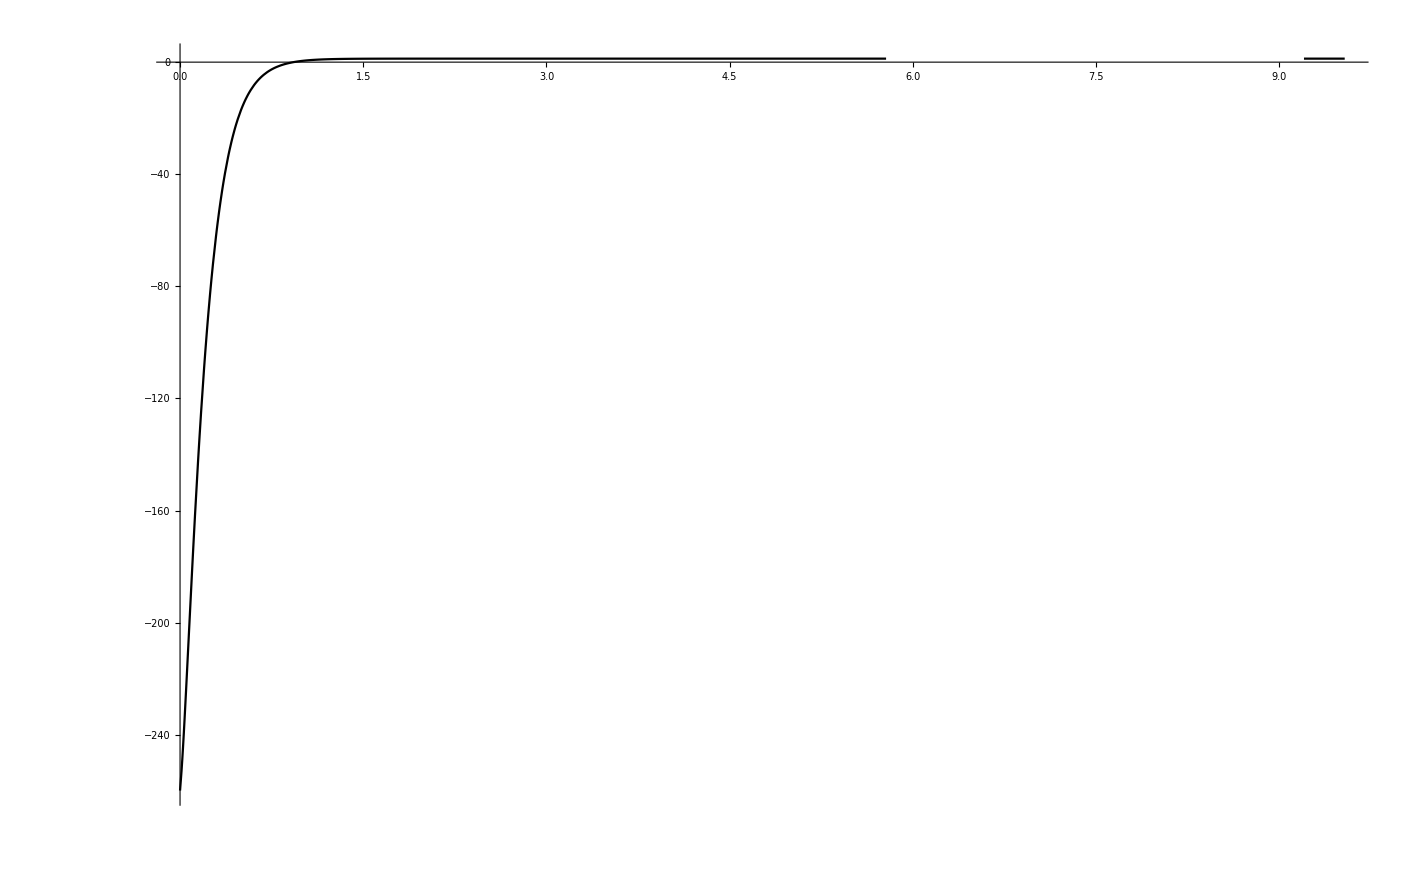

```mathematica
Plot[SrateNormalizedB [t,10^100,1],{t,0,20},PlotStyle->Black,PlotRange->All]
```

## Limiting Behavoirs

```mathematica
SrateNormalizedLate[b_,γ_]:=Assuming[assum,FullSimplify[Limit[SrateNormalized[xb,b,γ],xb->1]]]
```

```mathematica
SrateNormalizedLate2 = SrateNormalizedLate[b,γ]
```

5/4-Log[1+b^4]/(4 b^4)

```mathematica
Series[SrateNormalizedLate[b,γ],{b,0,16}]
```

1+b^4/8-b^8/12+b^12/16-b^16/20+O[b]^17

```mathematica
Series[SrateNormalizedLate[b,γ],{b,∞,16}]
```

5/4+Log[1/b]/b^4-1/(4 b^8)+1/(8 b^12)-1/(12 b^16)+O[1/b]^17

```mathematica
Assuming[assum,FullSimplify[Limit[SrateNormalizedLate[b,γ],b->∞]/Limit[SrateNormalizedLate[b,γ],b->0]]]
```

5/4

```mathematica
SrateNormalizedLate2
```

5/4-Log[1+b^4]/(4 b^4)

```mathematica
Limit[SrateNormalizedLate2,b->0]
```

1